```mathematica
(* setting the parameters for the forward binomial tree *)
(* initial stock price *) S0=100; (* mean rate of return *) α=0.10;
(* volatility *)σ=0.3; (* dividend yield *) δ=0; (* continuously compounded interest rate *)r=0.04; (* time horizon *) T=1; (* number of periods *) n=1;
```

```mathematica
(* length of every period *) h=T/n
```

1

```mathematica
(* up-down factors *) 
(* up factor *) u = E^((r-δ)*h+σ*Sqrt[h])
```

1.40495

```mathematica
(* down factor *) d = E^((r-δ)*h-σ*Sqrt[h])
```

0.771052

```mathematica
(* risk-neutral probability *) pstar=1/(1+E^(σ*Sqrt[h]))
```

0.425557

```mathematica
(* "true" probability *) p=(E^((α-δ)*h)-d)/(u-d)
```

0.527089

```mathematica
(* drawing the trees of up&down steps under the "true" probability *)

(* drawing Bernoulli trials *) LBern=RandomVariate[BernoulliDistribution[p],n]
```

{0}

```mathematica
{0}
```

{0}

```mathematica
(* cointosses from Bernoulli trials *) LCoinToss=-1+2*LBern
```

{-1}

```mathematica
(* prepending the origin *) LWalk=Prepend[Accumulate[LCoinToss],0]
```

{0,-1}

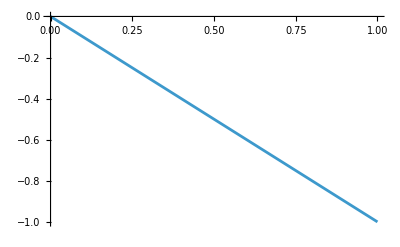

```mathematica
(* plotting the walk *) WalkToPlot[w_]:=Table[{i-1,w[[i]]}, {i,1,Length[w]}]; WalkToPlot[LWalk]; ListLinePlot[WalkToPlot[LWalk]]
```

```mathematica
(* more periods *)n=10
```

10

0.507971

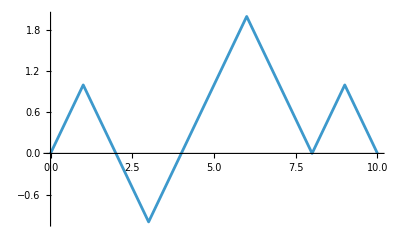

```mathematica
(* length of every period *) h=T/n; (* up factor *) u = E^((r-δ)*h+σ*Sqrt[h]); (* down factor *) d = E^((r-δ)*h-σ*Sqrt[h]); (* "true" probability *)p=(E^((α-δ)*h)-d)/(u-d)(* drawing the trees of up&down steps under the "true" probability *)

(* drawing Bernoulli trials *) LBern=RandomVariate[BernoulliDistribution[p],n]; (* cointosses from Bernoulli trials *) LCoinToss=-1+2*LBern; (* prepending the origin *) LWalk=Prepend[Accumulate[LCoinToss],0]; (* plotting the walk *) WalkToPlot[w_]:=Table[{i-1,w[[i]]}, {i,1,Length[w]}]; WalkToPlot[LWalk]; ListLinePlot[WalkToPlot[LWalk]]
```

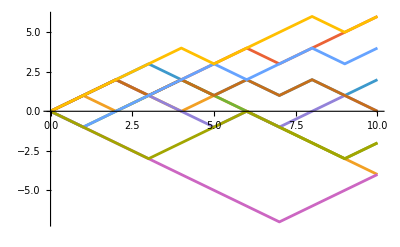

```mathematica
(* more simulated paths *)nsim=10;
(* drawing Bernoulli trials *) LBernSims=Table[RandomVariate[BernoulliDistribution[p],n], {nsim}]; (* cointosses from Bernoulli trials *) LCoinTossSims=-1+2*LBernSims ; (* prepending the origin *) LWalkSims=Table[Prepend[Accumulate[LCoinTossSims[[i]]],0],{i,1,nsim}];
 (* plotting the walk *) PlotFormat=Table[WalkToPlot[LWalkSims[[i]]], {i,1,nsim}];  ListLinePlot[PlotFormat]
```

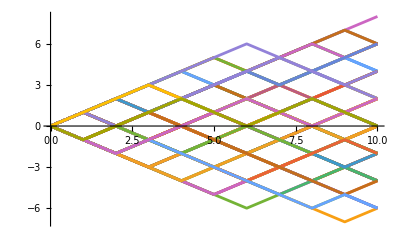

```mathematica
(* even more simulated paths *)nsim=100;
(* drawing Bernoulli trials *) LBernSims=Table[RandomVariate[BernoulliDistribution[p],n], {nsim}]; (* cointosses from Bernoulli trials *) LCoinTossSims=-1+2*LBernSims ; (* prepending the origin *) LWalkSims=Table[Prepend[Accumulate[LCoinTossSims[[i]]],0],{i,1,nsim}];
 (* plotting the walk *) PlotFormat=Table[WalkToPlot[LWalkSims[[i]]], {i,1,nsim}];  ListLinePlot[PlotFormat]
```

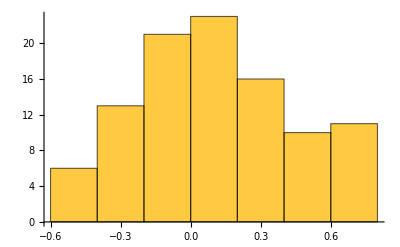

0.0494868

```mathematica
(* What are the simulated returns? *)
(* height of the final position *) htSims=Table[LWalkSims[[i,n+1]], {i,1,nsim}];(* number of steps up *) upstepsSims= (htSims+n)/2;(* number of steps down *) downstepsSims= n-upstepsSims; (* from cointosses to realized returns *) ReturnSims=Table[Log[u^upstepsSims[[i]]*d^downstepsSims[[i]]], {i,1,nsim}] ;
(* histogram of simulated realized returns *) Histogram[ReturnSims,bspec=50]
hatalpha=Mean[ReturnSims]
```

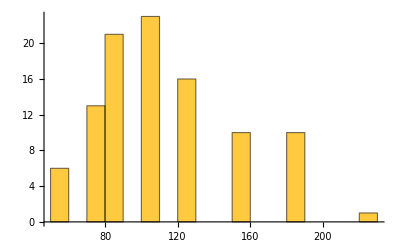

110.767

```mathematica
(* What are the simulated stock prices? *) S0=100; (* from cointosses to stock prices *) S1Sims=Table[S0*u^upstepsSims[[i]]*d^downstepsSims[[i]], {i,1,nsim}] ;(* histogram of simulated stock prices *) Histogram[S1Sims,bspec=50]
Mean[S1Sims]
```

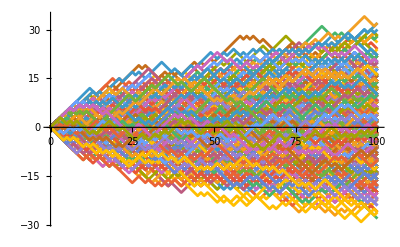

```mathematica
(* lots of periods *) n=100;(* length of every period *) h=T/n; (* up factor *) u = E^((r-δ)*h+σ*Sqrt[h]); (* down factor *) d = E^((r-δ)*h-σ*Sqrt[h]); (* "true" probability *)p=(E^((α-δ)*h)-d)/(u-d);

(* even more simulated paths *)nsim=1000;
(* drawing Bernoulli trials *) LBernSims=Table[RandomVariate[BernoulliDistribution[p],n], {nsim}]; (* cointosses from Bernoulli trials *) LCoinTossSims=-1+2*LBernSims ; (* prepending the origin *) LWalkSims=Table[Prepend[Accumulate[LCoinTossSims[[i]]],0],{i,1,nsim}];
 (* plotting the walk *) PlotFormat=Table[WalkToPlot[LWalkSims[[i]]], {i,1,nsim}];  ListLinePlot[PlotFormat]
```

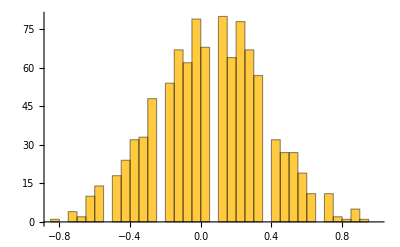

0.05032

```mathematica
(* What are the simulated returns? *)
(* height of the final position *) htSims=Table[LWalkSims[[i,n+1]], {i,1,nsim}];(* number of steps up *) upstepsSims= (htSims+n)/2;(* number of steps down *) downstepsSims= n-upstepsSims; (* from cointosses to realized returns *) ReturnSims=Table[Log[u^upstepsSims[[i]]*d^downstepsSims[[i]]], {i,1,nsim}] ;
(* histogram of simulated realized returns *) Histogram[ReturnSims,bspec=30]
hatalpha=Mean[ReturnSims]
```

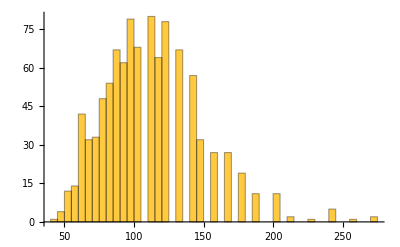

110.279

```mathematica
(* What are the simulated stock prices? *) S0=100; (* from cointosses to stock prices *) S1Sims=Table[S0*u^upstepsSims[[i]]*d^downstepsSims[[i]], {i,1,nsim}] ;(* histogram of simulated stock prices *) Histogram[S1Sims,bspec=50]
Mean[S1Sims]
```